```mathematica
Reduce[a+Sqrt[b]≤0,{a,b}]
```

(a<0&&0≤b≤a^2)||(a==0&&b==0)

```mathematica
Reduce[3(1-z^4/zp^4-1/4/λ)<32Pi l^2μ^2z^4(zp^2-z^2)&&0<1-4λ<(1-(32Pi l^2μ^2z^4(zp^2-z^2))/(3(1-z^4/zp^4-1/4/λ)))^2&&zp>0&&0<z≤zp&&l>0&&μ>0&&0<λ≤1/4,{λ,l,μ,zp,z}]
```

0<λ<1/4&&l>0&&μ>0&&zp>0&&0<z≤zp

```mathematica
BooleanConvert[Reduce[1-Sqrt[b-c Sqrt[d]]≥0&&c≤0&&d≥0,{b,c,d}],"DNF"]
```

(b==1&&c==0&&d≥0)||(b==1&&d==0&&c<0)||(c==0&&0≤b<1&&d≥0)||(0≤b<1&&0≤d≤(1-2 b+b^2)/c^2&&c<0)||(b^2/c^2≤d≤(1-2 b+b^2)/c^2&&b<0&&c<0)

```mathematica
Reduce[0≤1-4λ≤ (1-3λ/(8Pi l^2μ^2)(zp^2+z^2)/(zp^4 z^4))^2&&0<z<zp&&0≤1-4λ(1-z^4/zp^4)+32Pi l^2μ^2/3z^4(zp^2-z^2)&&μ>0&&l>0&&zp>0,{λ,l,μ,zp,z}]
```

(λ<0&&l>0&&μ>0&&((0<zp≤Root[9 λ-24 l^2 π μ^2 #1^6+64 l^4 π^2 μ^4 #1^12&,2]&&0<z<zp)||(zp>Root[9 λ-24 l^2 π μ^2 #1^6+64 l^4 π^2 μ^4 #1^12&,2]&&0<z≤Root[9 zp^4 λ+18 zp^2 λ #1^2+(9 λ-48 l^2 π zp^6 μ^2) #1^4-48 l^2 π zp^4 μ^2 #1^6+256 l^4 π^2 zp^8 μ^4 #1^8&,2])))||(λ==0&&l>0&&μ>0&&zp>0&&0<z<zp)||(0<λ<1/4&&l>0&&μ>0&&((0<zp≤Root[9 λ-24 l^2 π μ^2 #1^6+64 l^4 π^2 μ^4 #1^12&,3]&&0<z<zp)||(Root[9 λ-24 l^2 π μ^2 #1^6+64 l^4 π^2 μ^4 #1^12&,3]<zp≤Root[9 λ-24 l^2 π μ^2 #1^6+64 l^4 π^2 μ^4 #1^12&,4]&&0<z≤Root[9 zp^4 λ+18 zp^2 λ #1^2+(9 λ-48 l^2 π zp^6 μ^2) #1^4-48 l^2 π zp^4 μ^2 #1^6+256 l^4 π^2 zp^8 μ^4 #1^8&,3])||(zp>Root[9 λ-24 l^2 π μ^2 #1^6+64 l^4 π^2 μ^4 #1^12&,4]&&(0<z≤Root[9 zp^4 λ+18 zp^2 λ #1^2+(9 λ-48 l^2 π zp^6 μ^2) #1^4-48 l^2 π zp^4 μ^2 #1^6+256 l^4 π^2 zp^8 μ^4 #1^8&,3]||Root[9 zp^4 λ+18 zp^2 λ #1^2+(9 λ-48 l^2 π zp^6 μ^2) #1^4-48 l^2 π zp^4 μ^2 #1^6+256 l^4 π^2 zp^8 μ^4 #1^8&,4]≤z<zp))))||(λ==1/4&&l>0&&μ>0&&zp>0&&0<z<zp)

```mathematica
DSolve[D[z[t],t]^2==f[z[t]],z[t],t]
```

{{z[t]→InverseFunction[∫_1^#1 1/(√f[K[1]])ⅆK[1]&][-t+C[1]]},{z[t]→InverseFunction[∫_1^#1 1/(√f[K[2]])ⅆK[2]&][t+C[1]]}}

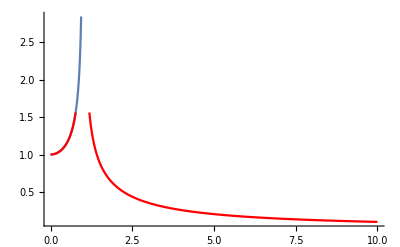

```mathematica
Show[
Plot[1/Sqrt[1-x^2],{x,0,10}],
Plot[1/Sqrt[Abs[1-x^2]],{x,0,10},PlotStyle->Red],PlotRange->All,AxesOrigin->{0,0}
]
```

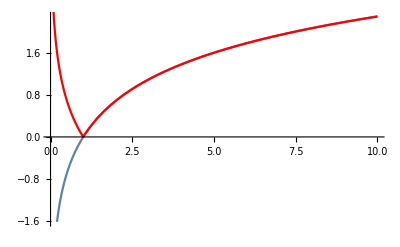

```mathematica
Show[
Plot[Log[x],{x,0,10}],
Plot[Abs[Log[x]],{x,0,10},PlotStyle->Red]
]
```

```mathematica
Reduce[((1-(1+zh^2μ^2)(z/zh)^4)+zh^2μ^2(z/zh)^6≥0&&(6zh^2μ^2z^5/zh^6-(1+zh^2μ^2)4z^3/zh^4≤0))/.{zh->1,μ->0.25}//N,{z}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

z≤-4.11634||0≤z≤1.